```mathematica
F[x_] = 1/(1+x^4)*1/Sqrt[Pi]
```

1/(√π (1+x^4))

```mathematica
Integrate[F[x],x]
```

(-2 ArcTan[1-√2 x]+2 ArcTan[1+√2 x]-Log[1-√2 x+x^2]+Log[1+√2 x+x^2])/(4 √(2 π))

```mathematica
Simplify[(-2 ArcTan[1-√2 x]+2 ArcTan[1+√2 x]-Log[1-√2 x+x^2]+Log[1+√2 x+x^2])/(4 √(2 π))]
```

(-2 ArcTan[1-√2 x]+2 ArcTan[1+√2 x]-Log[1-√2 x+x^2]+Log[1+√2 x+x^2])/(4 √(2 π))

```mathematica
Integrate[F[x],{x,-Infinity,+Infinity}]
```

√(π/2)

```mathematica
F[-Infinity]
```

0

```mathematica
G[x_]=(-2 ArcTan[1-√2 x]+2 ArcTan[1+√2 x]-Log[1-√2 x+x^2]+Log[1+√2 x+x^2])/(4*Pi)
```

(-2 ArcTan[1-√2 x]+2 ArcTan[1+√2 x]-Log[1-√2 x+x^2]+Log[1+√2 x+x^2])/(4 π)

Infinity::indet: Indeterminate expression 1+-∞+∞ encountered.

Indeterminate

```mathematica
c
```

-1/2

```mathematica
F[x_] = 1/(1+1/16*x^4)*1/Sqrt[Pi]
```

1/(√π (1+x^4/16))

```mathematica
Integrate[F[x],x]
```

(-2 ArcTan[1-x/(√2)]+2 ArcTan[1+x/(√2)]-Log[4-2 √2 x+x^2]+Log[4+2 √2 x+x^2])/(2 √(2 π))

```mathematica
Simplify[%11]
```

-0.237212 ArcTan[1.-1.18921 x]+0.237212 ArcTan[1.+1.18921 x]-0.118606 Log[1.41421-1.68179 x+1. x^2]+0.118606 Log[1.41421+1.68179 x+1. x^2]

```mathematica
PlF[x_] = 1/(1+1/16*x^4)*1/Sqrt[Pi]
```

```mathematica
Integrate[F[x],{x,-Infinity,+Infinity}]
```

√(2 π)

```mathematica
G[x_]=(-2 ArcTan[1-x/(√2)]+2 ArcTan[1+x/(√2)]-Log[4-2 √2 x+x^2]+Log[4+2 √2 x+x^2])/2
```

1/2 (-2 ArcTan[1-x/(√2)]+2 ArcTan[1+x/(√2)]-Log[4-2 √2 x+x^2]+Log[4+2 √2 x+x^2])

```mathematica
Limit[G[x],x->-Infinity]
```

-π

```mathematica
N[-π/°]
```

-180.

```mathematica
L[x_]=(-2 ArcTan[1-x/(√2)]+2 ArcTan[1+x/(√2)]-Log[4-2 √2 x+x^2]+Log[4+2 √2 x+x^2])/2+Pi
```

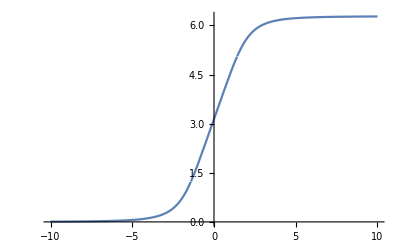

```mathematica
Plot[L[x],{x,-10,10}]
```

```mathematica
L[-5]
```

π+1/2 (2 ArcTan[1-5/(√2)]-2 ArcTan[1+5/(√2)]+Log[29-10 √2]-Log[29+10 √2])

```mathematica
N[(π+1/2 (2 ArcTan[1-5/(√2)]-2 ArcTan[1+5/(√2)]+Log[29-10 √2]-Log[29+10 √2]))/°]
```

3.41989

```mathematica
N[L[-16]]
```

0.00184123

```mathematica
N[L[-1.64]]
```

0.99163

```mathematica
NumberForm[0.9916299629063916,16]
```

0.991629962906392

```mathematica
H[x_]=(-2 ArcTan[1-√2 x]+2 ArcTan[1+√2 x]-Log[1-√2 x+x^2]+Log[1+√2 x+x^2])/(4*Pi)+1/2
```

1/2+(-2 ArcTan[1-√2 x]+2 ArcTan[1+√2 x]-Log[1-√2 x+x^2]+Log[1+√2 x+x^2])/(4 π)

```mathematica
H[10]
```

1/2+(-2 ArcTan[1-10 √2]+2 ArcTan[1+10 √2]-Log[101-10 √2]+Log[101+10 √2])/(4 π)

```mathematica
N[1/2+(-2 ArcTan[1-10 √2]+2 ArcTan[1+10 √2]-Log[101-10 √2]+Log[101+10 √2])/(4 π)]
```

0.99985

```mathematica
N[L[10]]
```

6.27565

```mathematica
H[0]
```

1/2

```mathematica
L[0]
```

π